Do::nliter: Non-list iterator DefaultFont→{font,textsz} at position 2 does not evaluate to a real numeric value.

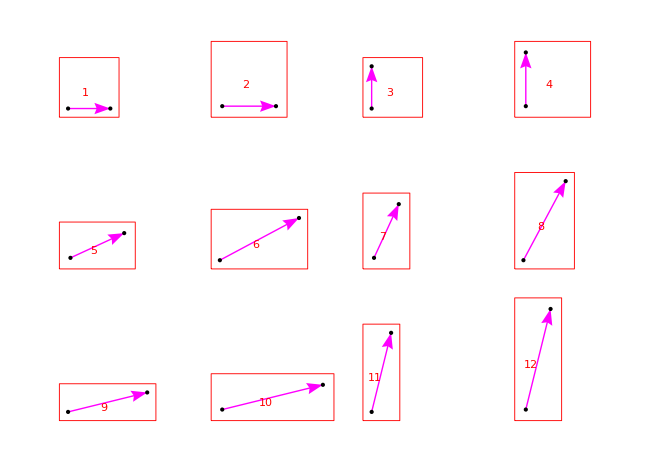

Syntax::sntxf: "" cannot be followed by "(* fibo-hilbert.m".

If::argb: If called with 6 arguments; between 2 and 4 arguments are expected.

p0

If::argb: If called with 6 arguments; between 2 and 4 arguments are expected.

p0

If::argb: If called with 6 arguments; between 2 and 4 arguments are expected.

General::stop: Further output of If::argb will be suppressed during this calculation.

p0

p0

p0

Syntax::sntxf: "" cannot be followed by "(* fibo-hilbert.m".

```mathematica
(* fibo-hilbert.m
   V.O. version 2002/12/14
*)
 
(****************** params *******************)
SetOptions[Graphics, ImageSize -> {650, Automatic}];

dbgInflation = False;
dbgInflation = True;

If[dbgInflation,
  niter:= 5;
  labelTileTypes = False;
  labelTileTypes = True;
  labelOrdinalNumber = True;
  labelOrdinalNumber = False;
,(*ELSE*)
  niter:= 10;
  labelTileTypes = False;
  labelTileTypes = True;
  labelOrdinalNumber = False;
  labelOrdinalNumber = True;
]

showGraphics = False;
showGraphics = True;

showTileShape = False;
showTileShape = True;
tileShapeCol = Red;
tileShapeTh = .001;

showRefPt = True;
showRefPt = False;
refPtCol = Yellow;

showSamplingPt = True;
showSamplingPt = False;
samplingPtCol = Yellow;

showThVal = True;
showThVal = False;
showThValTxt = True;
showThValTxt = False;

showdir = False;
showdir = True;

lbl = "fibo-hilbert";

dbg = True;
dbg = False;

symbolicForm  = False;
  cutOutOfRangeFlag = False;

font = "Courier-Bold"; textsz = 12;
{{xmin, xmax},{ymin, ymax}} = {{0,1},{0,1}};
rng = {{xmin, xmax},{ymin, ymax}};
epsilon = 10.^(-25);
(****************** end of params *******************)

(****************** constants *******************)
If[symbolicForm, tau = (1+Sqrt[5])/2, tau = 1.618033988749895];
stau:=Sqrt[tau];
tau1:=1/tau;
tau2:=tau^2;
zero = {0,0};

If[symbolicForm,
  hvect = Table[rotatedaround[{1,0},zero, (i) Pi/2], {i,4}]//Simplify;
  vvect = Table[rotatedaround[{0,1},zero, (i) Pi/2], {i,4}]//Simplify;
,(*ESLE*)
  hvect = Table[rotatedaround[{1,0},zero, (i) Pi/2], {i,4}]//N;
  vvect = Table[rotatedaround[{0,1},zero, (i) Pi/2], {i,4}]//N;
];
  
(*--------- tile data -----------*)

basicInflationSchemes = {
  {{0, zero}},						(*1*)
  {{0, zero},{3,{1/tau,1}}},				(*2*)
  {{0, zero}},						(*3*)
  {{0, zero},{1,{1,1/tau}}},				(*4*)
  {{0, zero}},						(*5*)
  {{0, zero},{0,{stau 1/tau,0}}},			(*6*)
  {{0, zero}},						(*7*)
  {{0, zero},{0,{0,stau 1/tau}}},			(*8*)
  {{0, zero}},						(*9*)
  {{0, zero},{3,{1,1/tau}}},				(*10*)
  {{0, zero}},						(*11*)
  {{0, zero},{1,{1/tau,1}}} 				(*12*)
}; (* basicInflationSchemes *)

(* inflationRules, tileShapes, tileSamplingPts are approximant-dependent *)

inflationRules = {
  {1,{2}},		(*1*)
  {2,{8,9}},		(*2*)
  {3,{4}},		(*3*)
  {4,{6,11}},		(*4*)
  {5,{6}},		(*5*)
  {6,{2,7}},		(*6*)
  {7,{8}},		(*7*)
  {8,{4,5}},		(*8*)
  {9,{10}},		(*9*)
  {10,{6,3}},		(*10*)
  {11,{12}},		(*11*)
  {12,{8,1}}		(*12*)
}; (* inflationRules *)
tileShapes = {
  1/stau{{0,0},{1,0},{1,1},{0,1}},		(* 1 sq*)
  {{0,0},{1,0},{1,1},{0,1}},			(* 2 sq*)
  1/stau{{0,0},{1,0},{1,1},{0,1}},		(* 3 sq*)
  {{0,0},{1,0},{1,1},{0,1}},			(* 4 sq*)
  {{0,0},{1,0},{1,1/tau},{0,1/tau}},		(* 5 1/tau*)
  stau{{0,0},{1,0},{1,1/tau},{0,1/tau}},	(* 6 1/tau*)
  {{0,0},{1/tau,0},{1/tau,1},{0,1}},		(* 7 1/tau*)
  stau{{0,0},{1/tau,0},{1/tau,1},{0,1}},	(* 8 1/tau*)
  stau{{0,0},{1,0},{1,1/tau2},{0,1/tau2}},	(* 9 1/tau2*)
  tau{{0,0},{1,0},{1,1/tau2},{0,1/tau2}},	(* 10 1/tau2*)
  stau{{0,0},{1/tau2,0},{1/tau2,1},{0,1}},	(* 11 1/tau2*)
  tau{{0,0},{1/tau2,0},{1/tau2,1},{0,1}} 	(* 12 1/tau2*)
}; (* tileShapes *)

tileSamplingPts = {
  {0,0}, {0,0}, {0,0}, {0,0},
  {0,0}, {0,0}, {0,0}, {0,0}
};

tileAreaCoefs = {
  {0},		(*1*)
  {0,1/tau},	(*2*)
  {0},		(*3*)
  {0,1/tau},	(*4*)
  {0},		(*5*)
  {0,1/tau},	(*6*)
  {0},		(*7*)
  {0,1/tau},	(*8*)
  {0},		(*9*)
  {0,1/tau},	(*10*)
  {0},		(*11*)
  {0,1/tau}	(*12*)
};

(*--------- end of tile data -----------*)

(****************** end of constants *******************)

(**************** System-dependent setup ******************)
If[$System == "Microsoft Windows",
  SetDirectory["c:\\3d"];
  epsOut:=Export[#1,#2,"EPS"]&; (* epsOut[fname,graph] *)
  (*epsOut:=Identity[#1]&;*)
,(*ELSE: Linux, Unix *)
  AppendTo[$Path,$HomeDirectory<>"/math"];
  epsOut:=Display["!psfix -width 5 -lmarg 0 > "<> #1,#2] &; (* epsOut[fname,graph] *)
  epsOut:=Display["!psfix -width 9 -lmarg 0 > "<> #1,#2] &; (* epsOut[fname,graph] *)
];
pdfOut:=Export[#1,#2,"PDF"]&; (* pdfOut[fname,graph] *)
pictOut:=Export[#1,#2,"PICT"]&; (* pictOut[fname,graph] *)
tiffOut:=Export[#1,#2,"TIFF",ImageSize->{512,512}]&; (* tiffOut[fname,graph] *)
date:= ToString[Date[][[1]]]<>"/"<>ToString[Date[][[2]]]<>"/"<>
        ToString[Date[][[3]]]<>"_"<>ToString[Date[][[4]]]<>":"<>
        ToString[Date[][[5]]];
Off[Solve::"ifun"]; Off[InverseFunction::"ifun"];
SetOptions["stdout", PageWidth -> 100];
pid=ToString[$ProcessID];
(**************** end of System-dependent setup ******************)


(****************** procedure *******************)
dbgPrint[x__]:=If[dbg,Print[x]]

mod4[x_]:=Mod[x-1,4]+1

euclidlen[z_]:= Sqrt[ Plus@@(z^2) ]
euclidlen::usage =
  "euclidlen[z_]\nEuclidian length of vector z\n in n-dim space";

rotatedaround[pt1_, pt2_, alpha_]:=Block[{a},
(* gives a point which is pt1 rotated around pt2 by angle alpha *)
    If [pt1 == pt2, Return[pt1]];
    a = ArcTan[(pt1-pt2)[[1]],(pt1-pt2)[[2]]];
    Return[ pt2 + euclidlen[pt1-pt2] {Cos[a+alpha], Sin[a+alpha]} ]
]; (* rotatedaround *)
rotatedaround::usage =
"rotatedaround[pt1,pt2,alpha] : Point pt1 rotated around pt2 by angle alpha";

rotatedaroundandscaled[pt1_, pt2_, alpha_, k_]:=
Block[{res, a},
    If [pt1 == pt2, Return[pt1]];
    a = ArcTan[(pt1-pt2)[[1]],(pt1-pt2)[[2]]];
    Return[ pt2 + k euclidlen[pt1-pt2] {Cos[a+alpha], Sin[a+alpha]} ]
]; (* rotatedaroundandscaled *)

arr[{from_,to_}]:= (*** arrow, compatible with Line[{pt1,pt2}] ***)
Block[{v1,v2,len,ka1=.07,ka2=.025,ka3=.06,ka},
    len = euclidlen[to - from]//N;
    v1 = (to - from) / len; v2 = {-v1[[2]], v1[[1]]};
    ka = 3 / tau^(iter/2.);
    {Line[{to-.05*ka*v1,from}],Polygon[{to,to-ka1 ka v1 - ka2 ka v2,to-ka3 ka v1,
	    to -ka1 ka v1 + ka2 ka v2}]}
]; (* arr *)


getFigure[tileType_,refPt_,dir_,scale_,params_]:=
  {tileType,refPt,mod4[dir],scale,params}

(*getGLst[flst_]:=Map[getGFigure, flst, {1}]*)
getGLst[flst_]:=Block[{res={},i},
  Do[
    AppendTo[res,getGFigure[flst[[i]],i] ]
  ,{i,Length[flst]}];
  Return[res]
]

getGFigure[fig_,n_]:=Block[{gl={},tileType,refPt,dir,scale,params,cont,
bis(*basicInflationScheme*),z0,z1,z2,z3,t1,t3,col,scalefactor=3},
  If[dbgLst, Print["getGFigure ",++count,"/",lstlen," iter=",iter]];
  {tileType,refPt,dir,scale,{thval}} = fig;
  cont = {z0,z1,z2,z3} = getTileShape[fig];
  If[showdir,
    col = Magenta;
    Switch[tileType
      ,1, {t1,t3}={z1,z3}; du=(t1-z0)/tau^(scalefactor+1); dv=(t3-z0)/tau^(scalefactor+1); end=z1;
      ,2, {t1,t3}={z1,z3}; du=(t1-z0)/tau^(scalefactor+1); dv=(t3-z0)/tau^(scalefactor+1); end=z1;
      ,3, {t1,t3}={z3,z1}; du=(t1-z0)/tau^(scalefactor+1); dv=(t3-z0)/tau^(scalefactor+1); end=z3;
      ,4, {t1,t3}={z3,z1}; du=(t1-z0)/tau^(scalefactor+1); dv=(t3-z0)/tau^(scalefactor+1); end=z3;
      ,5, {t1,t3}={z1,z3}; du=(t1-z0)/tau^(scalefactor+1); dv=(t3-z0)/tau^(scalefactor); end=z2;
      ,6, {t1,t3}={z1,z3}; du=(t1-z0)/tau^(scalefactor+2); dv=(t3-z0)/tau^(scalefactor+1); end=z2;
      ,7, {t1,t3}={z3,z1}; du=(t1-z0)/tau^(scalefactor+1); dv=(t3-z0)/tau^(scalefactor); end=z2;
      ,8, {t1,t3}={z3,z1}; du=(t1-z0)/tau^(scalefactor+2); dv=(t3-z0)/tau^(scalefactor+1); end=z2;
      ,9, {t1,t3}={z1,z3}; du=(t1-z0)/tau^(scalefactor+2); dv=(t3-z0)/tau^(scalefactor); end=z2;
      ,10,{t1,t3}={z1,z3}; du=(t1-z0)/tau^(scalefactor+2); dv=(t3-z0)/tau^(scalefactor); end=z2;
      ,11,{t1,t3}={z3,z1}; du=(t1-z0)/tau^(scalefactor+2); dv=(t3-z0)/tau^(scalefactor); end=z2;
      ,12,{t1,t3}={z3,z1}; du=(t1-z0)/tau^(scalefactor+2); dv=(t3-z0)/tau^(scalefactor); end=z2;
    ];
    If[1 <= tileType <= 4,
      AppendTo[gl,{{col,arr[{z0+du+dv,end-du+dv}]},Point[z0+du+dv],Point[end-du+dv]}];
    ,(*ELSE*)
      AppendTo[gl,{{col,arr[{z0+du+dv,end-du-dv}]},Point[z0+du+dv],Point[end-du-dv]}];
    ];
  ]; (* If[showdir, *)
  If[showRefPt,
    AppendTo[gl,{refPtCol,Point[refPt]}];
  ];
  If[showSamplingPt,
    AppendTo[gl,{samplingPtCol,Point[getSamplingPt[fig]]}];
  ];
  If[showTileShape,
    AppendTo[gl,{tileShapeCol,Thickness[tileShapeTh],Line@@{Append[cont,First[cont]]}}];
    AppendTo[border,{tileShapeCol,Thickness[tileShapeTh],Line@@{Append[cont,First[cont]]}}];
  ];
  If[showThVal,
    AppendTo[gl,{GrayLevel[thval],Polygon@@{Append[cont,First[cont]]}}];
  ];
  If[showThValTxt,
    AppendTo[gl,Text[ToString[thval],refPt,{-1,-1}] ]
  ];
  If[labelOrdinalNumber, AppendTo[gl,Text[ToString[i],(z0+z2)/2,{-1,-1}] ] ];
  If[labelTileTypes, 
    AppendTo[gl,{Red,Text[ToString[inflationRules[[tileType,1]]],(z0+z2)/2,{1,1}]} ] ];
  Return[gl]
] (* getGFigure *)

ptinrangePlusMargin[{x_,y_}]:=(xmin-margin < x < xmax+margin && ymin-margin < y < ymax+margin)
ptinrange[{x_,y_}]:= (xmin < x < xmax && ymin < y < ymax)

decomposeFLst[flst_]:=Block[{res={},i,j,len=Length[flst],newlst},
  Do[
    If[!cutOutOfRangeFlag,
      res = Join[res, decomposeFig[flst[[i]] ] ];
    ,(*ELSE*)
      newlst = decomposeFig[flst[[i]] ];
      Do[
        newfig = newlst[[j]];
        If[ptinrangePlusMargin[newfig[[2]]], (*refPt*)
        AppendTo[res,newfig];
        ]
      ,{j,Length[newlst]}];
    ];
  ,{i,len}];
  If[dbg,Print["decomposeFLst: done. ",len,"->",Length[res]]];
  Return[res];
] (* decomposeFLst *)

decomposeFig[fig_]:=Block[{res={},tileType,refPt,dir,scale,params,
thval,newthval,bis,scheme,ddir,ku,kv,u,v,i},
  {tileType,refPt,dir,scale,params} = fig;
  {thval} = params;
  {scheme,bislst} = inflationRules[[tileType]];
  Do[
    bis = bislst[[i]];
    {ddir,{ku, kv}} = basicInflationSchemes[[scheme,i]];
    u = scale hvect[[mod4[dir] ]];
    v = scale vvect[[mod4[dir] ]];
    newthval = thval/tau + tileAreaCoefs[[tileType,i]];
    AppendTo[res,getFigure[bis,refPt + ku u + kv v,dir+ddir,scale/stau,{newthval}] ]
  ,{i,Length[bislst]}];
  Return[res]
] (* decomposeFigure *)

getSamplingPt[fig_]:=Block[{centers,ku,kv,u,v,tileType,refPt,dir,scale,params},
  {tileType,refPt,dir,scale,params} = fig;
  {ku,kv} = tileSamplingPts[[tileType]];
  u = scale hvect[[mod4[dir] ]];
  v = scale vvect[[mod4[dir] ]];
  Return[refPt + ku u + kv v]
] (* getSamplingPt *)

getFigVoronoiArea[fig_]:=convexPolygonArea[getVoronoi[fig]] 

convexPolygonArea[v_]:=
  Plus @@ Table[triArea[v[[1]],v[[i-1]],v[[i]]],{i,3,Length[v]}];

getFigBaryCentre[fig_]:= getBaryCentreFromShape[getVoronoi[fig]]

getBaryCentreFromShape[v_]:=Block[{triAreas,triCenters,center},
  triAreas=Table[triArea[v[[1]],v[[i-1]],v[[i]]],{i,3,Length[v]}];
  triCenters=Table[(v[[1]]+v[[i-1]]+v[[i]])/3,{i,3,Length[v]}];
  center = (Plus@@(triAreas triCenters))/(Plus@@triAreas);
  If[symbolicForm, center = center//Simplify, center = center//Chop];
  Return[center]
] (* getBaryCentreFromShape *)


triArea[z1_,z2_,z3_]:=Abs[Det[{z3-z1,z2-z1}]]/2;
triPositiveArea[z1_,z2_,z3_]:=Det[{z3-z1,z2-z1}]/2;
findequidistantPt[{x1_,y1_},{x2_,y2_},{x3_,y3_}]:=Block[{xsol,ysol,sol},
    sol=Solve[{L2[{x1,y1}-{xsol,ysol}]==L2[{x2,y2}-{xsol,ysol}]==L2[{x3,y3}-{xsol,ysol}]},{xsol,ysol}];
    Return[{Replace[xsol,sol[[1]]],Replace[ysol,sol[[1]]]}//Chop]
]

getTileShape:=getVoronoi;
getVoronoi[fig_]:=Block[{res={},tileType,refPt,dir,scale,params,u,v,coefs,vvertices},
  {tileType,refPt,dir,scale,params} = fig;
  u = scale hvect[[mod4[dir]]];
  v = scale vvect[[mod4[dir]]];
  coefs = tileShapes[[tileType]];
  vvertices = Plus@@Transpose[Map[Times[{u,v},#]&, coefs]];
  res = Plus[refPt,#]& /@ vvertices;
  Return[res]
];

grada[flst_,{xMin_,xMax_},{yMin_,yMax_}]:=
Block[{res={},i,len=Length[flst],x,y,inputVal,fig},
  Do[
    fig=flst[[i]];
    {{pType,sType,dir},refPt,mag,{thval}} = fig;
    {x,y} = getCenter[fig];
    If[xMin < x < xMax && yMin < y < yMax,
      inputVal = (x - xMin)/(xMax-xMin);
      If[inputVal > thval, AppendTo[res,Point[{x,y}] ] ];
    ];
  ,{i,len}];
  Return[res]
] (*grada*)

constLevel[thval_,flst_,{xMin_,xMax_},{yMin_,yMax_}]:=
Block[{res={},i,len=Length[flst],x,y,inputVal,fig},
  Do[
    fig=flst[[i]];
    {{pType,sType,dir},refPt,mag,{thval}} = fig;
    {x,y} = getCenter[fig];
    If[xMin < x < xMax && yMin < y < yMax,
      If[inputVal > thval-epsilon, AppendTo[res,Point[{x,y}] ] ];
    ];
  ,{i,len}];
  Return[res]
] (*constLevel*)

showThValues[flst_]:=Block[{res={},i,len=Length[flst],x,y,fig},
  Do[
    fig=flst[[i]];
    {{pType,sType,dir},refPt,mag,extra} = fig;
    {thval} = extra;
    {x,y} = getCenter[fig];
    AppendTo[res,{{Yellow,Point[{x,y}]},Text[ToString[thval],{x,y}] }];
  ,{i,len}];
  Return[res]
] (*showThValues*)

getThValues[flst_]:=Block[{res={},i,len=Length[flst],x,y,fig},
  Do[
    fig=flst[[i]];
    {{pType,sType,dir},refPt,mag,extra} = fig;
    {thval} = extra;
    {x,y} = getCenter[fig];
    AppendTo[res,thval];
  ,{i,len}];
  Return[res]
] (*showThValues*)

dumpSamplingPts[flst_,fname_]:=
Block[{i,x,y,res={},len=Length[flst],out,count=0,countmarg=0},
  out = OpenWrite[fname];
  Do[
    {x,y} = getSamplingPt[flst[[i]]]//Chop;
    dbgPrint[i,"/",len," -> ",{x,y}];
    If[ptinrange[{x,y}],
      count++;
      WriteString[out,ToString[CForm[x]]<>" "<>ToString[CForm[y]]<>" 0\n"];
      AppendTo[res,Point[{x,y}]];
      (*AppendTo[res,{Text[ToString[countmarg+count],{x,y},{-1,-1}]}];*)
    ,(*ELSE *)
      countmarg++;
      WriteString[out,ToString[CForm[x]]<>" "<>ToString[CForm[y]]<>" -1\n"];
      AppendTo[res,{Red,Point[{x,y}]} ];
      (*AppendTo[res,{Text[ToString[countmarg+count],{x,y},{-1,-1}]}];*)
    ]
  ,{i,len}];
  Close[out];
  dbgPrint["Written: ",count,"+",countmarg,"=",countmarg+count];
  Return[res]
] (* dumpSamplingPts *)

(*-----------------------------------------------------*)

(****************** end of procedures *******************)

(************* prog starts here *************)
iter = 0; dir = 0; flst = {}; margin=1;
border = {};

If[dbgInflation,
  rng = All;
  {px,py} = {2,-2}; n = 4;
  n = Ceiling[Sqrt[Length[inflationRules]]];
  Do[
    type = i;
    {x,y} = {px,py} {(i-1) - n Floor[(i-1)/n], Floor[(i-1)/n]};
    AppendTo[flst,getFigure[type,{x,y},dir,1,{0}]];
  ,{i,Length[inflationRules]}];
  gl = {getGLst[flst]};
  p = Show[Graphics[{gl}],AspectRatio->Automatic,
       DefaultFont->{font,textsz}];
  tileShapeCol = Blue;
  Do[
    iter = i;
    flst = decomposeFLst[flst];
    gl = getGLst[flst];
    p = Graphics[{border,gl}], DefaultFont->{font,textsz}, AspectRatio->Automatic,PlotRange->rng,PlotLabel->i];
    p//Print;
  ,{i,niter}]
,(*ELSE*)
  If[showGraphics,
    AppendTo[flst,getFigure[2,{0,0},dir,1,{0}]];
    gl = {getGLst[flst]};
    p = Show[Graphics[{gl}],AspectRatio->Automatic,
	 DefaultFont->{font,textsz}];
  ];
  tileShapeCol = RGBColor[0,1,1];
  Do[
    iter = i;
    plbl = ToString[lbl]<>" iter="<>ToString[iter]<>" "<>date;
    flst = decomposeFLst[flst];
    If[showGraphics,
      gl = getGLst[flst];
      p0 = Graphics[{gl}], DefaultFont->{font,textsz}, AspectRatio->Automatic,PlotRange->rng,PlotLabel->plbl ];
      Print[p0];
  ,{i,niter}];
]
```